```mathematica
ClearAll[F]; ClearAll[r]; ClearAll[F0]; ClearAll[σ]; ClearAll[U];
F[r_]:=F0*((2*(σ/r)^13)-((σ/r)^7));  //Simplify
"F(r) = "<>ToString[F[r],TraditionalForm]
F0=9.60*10^-11;
σ=3.50*10^-11;
"F(r) = "<>ToString[F[r],TraditionalForm]
U[r_]=Integrate[-F[r],r];
"U(r) = "<>ToString[U[r],TraditionalForm]  (* N2a *)
```

F(r) = TraditionalForm`F0\ (2\ σ^13/r^13 - σ^7/r^7)

F(r) = TraditionalForm`9.6×10^-11\ (2.36545×10^-136/r^13 - 6.43393×10^-74/r^7)

U(r) = TraditionalForm`1.89236×10^-147/r^12 - 1.02943×10^-84/r^6

```mathematica
r0=3.9286171690828048*10^-11;  (* MANUAL TRIAL-AND-ERROR *)  (* N2b *)
(* r0=FindRoot[F[r]==0,{r,3.92*10^-11}][[1,2]]; *)(* FindRoot[] does not appear to work worrectly in this case *)
"r0 = "<>ToString[r0,TraditionalForm]
"F("<>ToString[r0,TraditionalForm]<>") = "<>ToString[F[r0],TraditionalForm]<>
"  <<<=== CHECK: SHOULD BE VERY CLOSE TO ZERO"
"U("<>ToString[r0,TraditionalForm]<>") = "<>ToString[U[r0],TraditionalForm]
```

r0 = TraditionalForm`3.9286171690828045`*^-11

F(TraditionalForm`3.9286171690828045`*^-11) = TraditionalForm`5.329070518200751`*^-26  <<<=== CHECK: SHOULD BE VERY CLOSE TO ZERO

U(TraditionalForm`3.9286171690828045`*^-11) = TraditionalForm`-1.4×10^-22

lowerbound r0 = TraditionalForm`3.8`*^-11

upperbound r0 = TraditionalForm`4.`*^-11

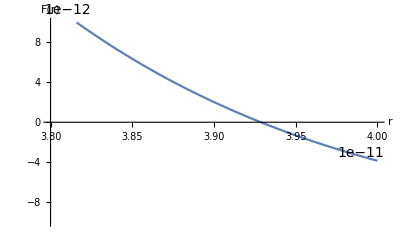

```mathematica
lowerbound r0=3.8*10^-11;
"lowerbound r0 = "<>ToString[lowerbound r0,TraditionalForm]
upperbound r0=4.0*10^-11;
"upperbound r0 = "<>ToString[upperbound r0,TraditionalForm]
graph F=Plot[F[r],{r,lowerbound r0,upperbound r0},PlotRange->{{lowerbound r0,upperbound r0},{-10^-11,10^-11}},AxesLabel->{r,"F(r)"}];
Show[graph F]
(* The graph below shows the force changing from repulsive to attractive at r0. *)
```

lowerbound r0 = TraditionalForm`3.535755452174524`*^-11

upperbound r0 = TraditionalForm`9.821542922707011`*^-11

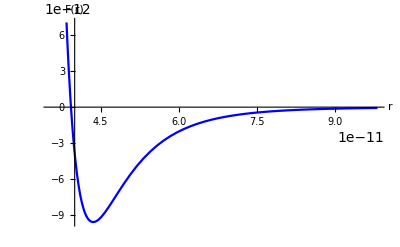

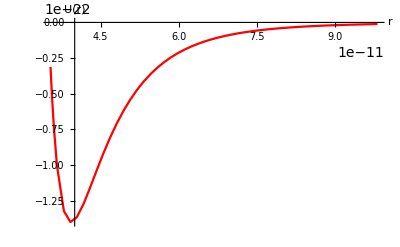

```mathematica
lowerbound r0=0.9*r0;
"lowerbound r0 = "<>ToString[lowerbound r0,TraditionalForm]
upperbound r0=2.5*r0;
"upperbound r0 = "<>ToString[upperbound r0,TraditionalForm]
graph F=Plot[F[r],{r,lowerbound r0,upperbound r0},
PlotRange->Automatic,AxesLabel->{r,"F(r)"},PlotStyle->Blue];
Show[graph F]
graph U=Plot[U[r],{r,lowerbound r0,upperbound r0},PlotRange->Automatic,AxesLabel->{r,"U(r)"},PlotStyle->Red];
Show[graph U]
(* The graphs below shows F[r] and U[r]. *)  (* N2c *)
```